{-0.000791139,0.0015804,0.00355591,0.0229068,0.0462268,0.0881771,0.163435,0.227723,0.281634,0.328038,0.70461,0.824336,0.90096,0.942015}

{2000,400,200,40,20,10,5,10/3,5/2,2,2/5,1/10,1/20,1/40}

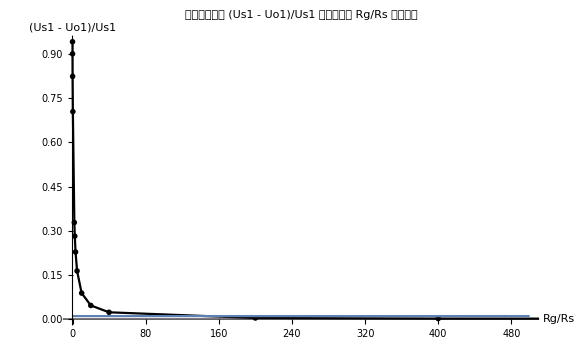

```mathematica
(* Exp2 *)
(* Data starts here *)
Rg = 100000;
Rs = {50, 250, 500, 2500, 5000, 10000, 20000, 30000, 40000, 50000, 250000, 1000000, 2000000, 4000000};
Us1 = {2.528, 2.531, 2.531, 2.532, 2.531, 2.529, 2.527, 2.525, 2.521, 2.518, 2.451, 2.408, 2.292, 2.104};
Uo1 = {2.530, 2.527, 2.522, 2.474, 2.414, 2.306, 2.114, 1.950, 1.811, 1.692, 0.724, 0.423, 0.227, 0.122};
graphY = (Us1 - Uo1)/Us1
graphX = Rg / Rs

f[x_] := 0.01;
graphData = Transpose[{graphX, graphY}];
 
(* Graph starts here *)
Show[ListPlot[graphData, PlotStyle->Black, PlotMarkers->{Style["X", 10]}],
ListLinePlot[graphData, PlotStyle->Black],
Plot[f[x], {x,0, 500}],
AxesLabel->{Style["Rg/Rs", 15, Bold], Style["(Us1  -  Uo1)/Us1", 15, Bold]},
PlotLabel-> Style["电压相对误差 (Us1  -  Uo1)/Us1 与电路参数 Rg/Rs 关系曲线", 18, FontFamily->"Hack", Bold],
AxesStyle->Directive[Arrowheads[0.05], 12],
ImageSize->Large]
```

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-Exp4/2.pdf",%185,"PDF"]
```

/Users/bbn/My/Git/PhyExam/2018-Exp4/2.pdf

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-Exp4/1.png",%185,"PNG"]
```

/Users/bbn/My/Git/PhyExam/2018-Exp4/1.png

{{0.,-0.0025},{0.2,-0.0015},{0.4,-0.0007},{0.6,-0.001},{0.8,-0.0001},{1.,-0.0009},{1.2,-0.0003},{1.4,-0.0008},{1.6,-0.0003},{1.8,0.0002},{2.,0.0003}}

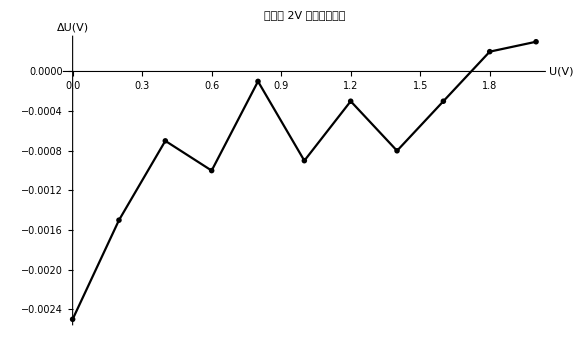

```mathematica
(* Exp3 *)
(* Data Starts here *)
us1 = Range[0.0, 2.0, 0.2];
uo1 = {0.0025, 0.2015, 0.4007, 0.6010, 0.8001, 1.0009, 1.2003, 1.4008, 1.6003, 1.7998, 1.9997};
deltaU = us1 - uo1;
data = Transpose[{us1, deltaU}]
Show[ListPlot[data, PlotStyle->Black, PlotMarkers->{Style["X", 10]}],
ListLinePlot[data, PlotStyle->Black],
AxesLabel->{Style["U(V)", 15, Bold], Style["ΔU(V)", 15, Bold]},
PlotLabel-> Style["组装表 2V 量程校准曲线", 18, FontFamily->"Hack", Bold],
ImageSize->Large]
```

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-Exp4/1.jpg",%312,"JPEG"]
```

/Users/bbn/My/Git/PhyExam/2018-Exp4/1.jpg

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-Exp4/1.pdf",%312,"PDF"]
```

/Users/bbn/My/Git/PhyExam/2018-Exp4/1.pdf

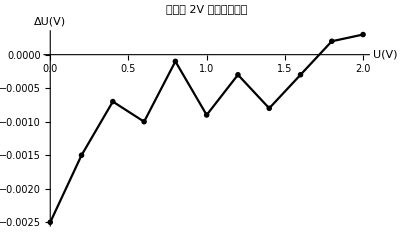

```mathematica
Show[%312,ImageSize->Full]
```

```mathematica
Export["/Users/bbn/My/Git/PhyExam/2018-Exp4/2.jpg",%313,"JPEG"]
```

/Users/bbn/My/Git/PhyExam/2018-Exp4/2.jpg